# 3 - answers to selected challenges

## “Easy” interactivity | Using Manipulate

```mathematica
(*Challenge 1*)

countryTable[country_] := Module[
	{neighbours, neighbLife, neighbWealth, neighbNames},

	neighbours = Join[{country}, CountryData[country, "BorderingCountries"]];
	neighbNames = Map[CountryData[#, "Name"]&, neighbours];
	neighbLife = Map[QuantityMagnitude@CountryData[#, "LifeExpectancy"]&, neighbours];
	neighbWealth = Map[QuantityMagnitude@CountryData[#, "GDPPerCapita"]&, neighbours];
	
	Grid[Transpose[
			{Join[{"country"}, neighbNames],
			 Join[{"wealth [USD]"}, neighbWealth],
			 Join[{"life exp [years]"}, neighbLife]}],
	     Frame->All]			
]
```

```mathematica
countryTable["France"]
```

country | wealth [USD] | life exp [years]
France | 36855. | 82.2732
Andorra | 36988.6 | 82.51
Belgium | 41096.2 | 80.9927
Germany | 41936.1 | 80.6415
Italy | 30527.3 | 82.5439
Luxembourg | 102831. | 82.2927
Monaco | 163352. | 80.09
Spain | 26528.5 | 82.8317
Switzerland | 78812.7 | 82.8976

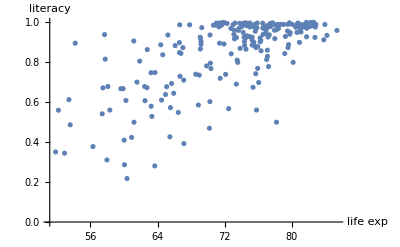

```mathematica
(*Challenge 2*)

countries = CountryData["Countries"];
names = Map[CountryData[#,"Name"]&, countries];
life = Map[CountryData[#,"LifeExpectancy"]&, countries];
literacy = Map[CountryData[#,"LiteracyFraction"]&, countries];
popupData = Map[PopupWindow[{#⟦1⟧, #⟦2⟧}, countryTable[#⟦3⟧]]&,
				Transpose[{life,literacy,countries}]];
ttipData = Map[Tooltip[#⟦1⟧, #⟦2⟧]&,
               Transpose[{popupData, names}]];

ListPlot[ttipData,
	AxesLabel->{"life exp", "literacy"}]
```

```mathematica
(*Challenge 3*)

Manipulate[Module[
	{countries,names,life,literacy,avgLife,avgLiteracy,
	pts,ptsNotMissing,ptsFiltered},
	
	countries = CountryData["Countries"];
	names = Map[CountryData[#,"Name"]&, countries];
	life = Map[CountryData[#,"LifeExpectancy"]&, countries];
	literacy = Map[CountryData[#,"LiteracyFraction"]&, countries];

	pts = Transpose[{life,literacy}];
	ptsNotMissing = DeleteCases[pts, {_Missing, _} | {_, _Missing}];
	ptsFiltered = Select[ptsNotMissing, xmin < QuantityMagnitude[#⟦1⟧] < xmax && 
		ymin < QuantityMagnitude[#⟦2⟧] < ymax &];
		
	avgLife = Mean[ptsFiltered]⟦1⟧ // QuantityMagnitude;
	avgLiteracy = Mean[ptsFiltered]⟦2⟧ // QuantityMagnitude;
	avgLife = Mean[ptsFiltered]⟦1⟧ // QuantityMagnitude;
	avgLiteracy = Mean[ptsFiltered]⟦2⟧ // QuantityMagnitude;

	ListPlot[Transpose[{life, literacy}],
		AxesLabel->{"life exp", "literacy"},
		Epilog->{
			{RGBColor[1,1,0,0.3],
		     Rectangle[{xmin,ymin}, {xmax,ymax}]},
			Text[Grid[{{"avg life exp: ", avgLife},
				      {"avg literacy: ", avgLiteracy}}],
			     {80,0.15}]	
	}]],
	{{xmin, 55}, 50, 85},
	{{ymin, 0.2}, 0, 1},
	{{xmax, 70}, 50, 85},
	{{ymax, 0.8}, 0, 1}
]
```

## Options and enhancements of Manipulate

```mathematica
(* Challenge 1 *)

Manipulate[Module[
	{countriesM, x, y},
	
	countriesM = CountryData["Countries"];
	x = Map[CountryData[#, ToString[xname]]&, countriesM];
	y = Map[CountryData[#, ToString[yname]]&, countriesM];
	
	ListPlot[Transpose[{x, y}],
		AxesLabel->{ToString[xname], ToString[yname]}]],
		
	{xname, LiteracyFraction},
	{yname, LifeExpectancy}
]
```

```mathematica
(* Challenge 2 *)

Manipulate[Module[
	{countries,names,life,literacy,avgLife,avgLiteracy,
	 xmin, ymin, xmax, ymax, pts, ptsNotMissing, ptsFiltered},
	
	countries = CountryData["Countries"];
	names = Map[CountryData[#,"Name"]&, countries];
	life = Map[CountryData[#,"LifeExpectancy"]&, countries];
	literacy = Map[CountryData[#,"LiteracyFraction"]&, countries];
	
	xmin = ptmin⟦1⟧;
	ymin = ptmin⟦2⟧;
	xmax = ptmax⟦1⟧;
	ymax = ptmax⟦2⟧;
	
	pts = Transpose[{life,literacy}];
	ptsNotMissing = DeleteCases[pts, {_Missing, _} | {_, _Missing}];
	ptsFiltered = Select[ptsNotMissing, xmin < QuantityMagnitude[#⟦1⟧] < xmax && 
		ymin < QuantityMagnitude[#⟦2⟧] < ymax &];

	avgLife = Mean[ptsFiltered]⟦1⟧ // QuantityMagnitude;
	avgLiteracy = Mean[ptsFiltered]⟦2⟧ // QuantityMagnitude;

	ListPlot[Transpose[{life, literacy}],
		AxesLabel->{"life exp", "literacy"},
		Epilog->{
			{RGBColor[1,1,0,0.3],
		     Rectangle[ptmin, ptmax]},
			Text[Grid[{{"avg life exp: ", avgLife},
				      {"avg literacy: ", avgLiteracy}}],
			     {80,0.15}]	
	}]],
	{{ptmin, {55,0.2}}, {50,0}, {85,1}, Locator},
	{{ptmax, {70,0.8}}, {50,0}, {85,1}, Locator}
]
```

```mathematica
(* Challenge 3 *)

Manipulate[Module[
	{countries,names,life,literacy,avgLife,avgLiteracy,
	 xmin, ymin, xmax, ymax, pts, ptsNotMissing, ptsFiltered},
	
	countries = CountryData["Countries"];
	names = Map[CountryData[#,"Name"]&, countries];
	life = Map[CountryData[#,"LifeExpectancy"]&, countries];
	literacy = Map[CountryData[#,"LiteracyFraction"]&, countries];
	
	{xmin, ymin} = MapThread[Min, {ptmin, ptmax}];
	{xmax, ymax} = MapThread[Max, {ptmin, ptmax}];

	pts = Transpose[{life,literacy}];
	ptsNotMissing = DeleteCases[pts, {_Missing, _} | {_, _Missing}];
	ptsFiltered = Select[ptsNotMissing, xmin < QuantityMagnitude[#⟦1⟧] < xmax && 
		ymin < QuantityMagnitude[#⟦2⟧] < ymax &];

	avgLife = Mean[ptsFiltered]⟦1⟧ // QuantityMagnitude;
	avgLiteracy = Mean[ptsFiltered]⟦2⟧ // QuantityMagnitude;

	ListPlot[Transpose[{life, literacy}],
		AxesLabel->{"life exp", "literacy"},
		Epilog->{
			{RGBColor[1,1,0,0.3],
		     Rectangle[{xmin,ymin}, {xmax,ymax}]},
			Text[Grid[{{"avg life exp: ", avgLife},
				      {"avg literacy: ", avgLiteracy}}],
			     {80,0.15}]	
	}]],
	{{ptmin, {55,0.2}}, {50,0}, {85,1}, Locator},
	{{ptmax, {70,0.8}}, {50,0}, {85,1}, Locator}
]
```